## (#X): Packages:

## (#X.1): FeynCalc:

```mathematica
<<FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

## (#X): Good Mathematica Practice:

```mathematica
ClearAll["Global`*"];
ClearScalarProducts;
```

## (#X): Static Quantities:

### (#X.1): Static Quantities | CFFs

```mathematica
Realℋ=-0.897;
RealℋT=2.444;
Realℰ=-0.541;
RealℰT=2.207;
Imaginaryℋ=2.421;
ImaginaryℋT=1.131;
Imaginaryℰ=0.903;
ImaginaryℰT=5.383;
ℋ=Realℋ+I Imaginaryℋ;
ℋT=RealℋT+I ImaginaryℋT;
ℰ=Realℰ+I Imaginaryℰ;
ℰT=RealℰT+I ImaginaryℰT;
```

### (#X.2): Static Quantities | Form Factors:

```mathematica
GE=1/(1+-t/0.71)^2;
GM=2.79*GE;
F1=(GE-t/(4 M^2)GM)/(1-t/(4 M^2));
F2=(-GE+GM)/(1-t/(4 M^2));
```

### (#X.3): Static Quantities | Cross Section Prefactor

```mathematica
Prefactor = (Subscript[α, EM]^3 xB y^2)/(16 π^2 Q^4 √(1+γ^2));
```

## (#X): Substitutions:

## (#X.1): Kinematics:

### (#X.1): Kinematics Point 1 | “The Standard One”

```mathematica
kinematicSetting1={
y->0.49624,
M->0.938,
Q->Sqrt[1.82],
t->-0.17,
xB->0.34,
Subscript[α, EM]->1/137.036};
```

## (#X.2): Lightcone Choice:

### (#X.2): Lightcone Choice | BKM:

```mathematica
lightconeBKMSetting={α->1/2,β->1/2};
```

### (#X.3): Lightcone Choice | UVA:

```mathematica
lightconeBKMSetting={α->1,β->1};
```

## (#X.3): Others:

### (#X.3): Others | ξ

```mathematica
ξsub={ξ->xB/(2-xB)-(2 xB (2 M^2 xB^2 α+t (-1+xB) (1-2 α+xB (-1+β))))/((-2+xB)^2 (1+xB (-1+β))Q^2)};
```

## (#X): FeynCalc Computations:

## (#X.1): Compton Tensor:

```mathematica
ϵt[a_,b_]:=(Sqrt[2]*Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]])/(-Sqrt[Contract[Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]]*Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]]]]);
gt[a_,b_]:=Contract[ϵt[a,c]*ϵt[b,c]];

𝒯1[a_,b_]:=-1/2 gt[a,b];
𝒯1t[a_,b_]:=ⅈ/2 ϵt[a,b];
```

## (#X.2): Target Polarization Vector:

```mathematica
SL[μ_]:=M/(1+ξ)(-FV[n,μ]+SP[n,p]/M^2 FV[p,μ]);
STin[μ_]:=1/((1+ξ)Sqrt[-4M^2ξ^2-t(1-ξ^2)])(Contract[Eps[LorentzIndex[μ],LorentzIndex[ν],Momentum[p],Momentum[n]]*Eps[Momentum[n],Momentum[p],Momentum[pp],LorentzIndex[ν]]]);
STout[μ_]:=1/Sqrt[-4M^2ξ^2-t(1-ξ^2)] Eps[Momentum[n],Momentum[p],Momentum[pp],LorentzIndex[μ]];
```

## (#X.3): Leptonic Tensor:

### (#X.3.1): Leptonic Tensor | DVCS | Unpolarized Target

```mathematica
LDVCSunp=Simplify[DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].(GA[α1]/Q^2).SpinorU[k]]*SpinorUBar[kp].(GA[α2]/Q^2).SpinorU[k]]],{h^2==1}];
```

### (#X.3.2): Leptonic Tensor | DVCS | Polarized Target

```mathematica
LDVCSp=Simplify[-ⅈ*DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].(GA[α1]/Q^2).SpinorU[k]]*SpinorUBar[kp].(GA[α2]/Q^2).DiracMatrix[5].SpinorU[k]]],{h^2==1}];
```

### (#X.3.3): Leptonic Tensor | Interference | Unpolarized Target

```mathematica
LINTunp=Expand[Simplify[DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].GA[α2].SpinorU[k]]*Contract[SpinorUBar[kp].(GA[α1].((GS[kp]+GS[qp])/(2 SP[kp,qp])).GA[α]+GA[α].((GS[k]-GS[qp])/(-2SP[k,qp])).GA[α1]).SpinorU[k]]]]]];
```

### (#X.3.4): Leptonic Tensor | Interference | Polarized Target

```mathematica
LINTp=Expand[Simplify[-ⅈ*DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].GA[α2].SpinorU[k]]*Contract[SpinorUBar[kp].(GA[α1].((GS[kp]+GS[qp])/(2 SP[kp,qp])).GA[α]+GA[α].((GS[k]-GS[qp])/(-2SP[k,qp])).GA[α1]).DiracMatrix[5].SpinorU[k]]]]]];
```

## (#X): Scalar Coefficients:

## (#X.1): Twist-2 Coefficients

### (#X.1.1): Twist-2 Coefficients | DVCS | h^U:

```mathematica
hU=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1[α3,α1]]*𝒯1[α4,α2]*(-MT[α3,α4])]]]//TraditionalForm
```

((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

### h^UTilde

```mathematica
hUTilde=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1t[α3,α1]]*𝒯1t[α4,α2]*(-MT[α3,α4])]]] //TraditionalForm
```

((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

### h^(-,L)

```mathematica
hMinusL=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]+𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]]//TraditionalForm
```

0

### h^(+,U)

```mathematica
hPlusU=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]-𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]] //TraditionalForm
```

((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp]))/(√((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#X.1.5): Twist-2 Coefficients | Interference | Aiu

```mathematica
AINTunpc=Simplify[ScalarProductExpand[Contract[8*FV[p,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | Biu

```mathematica
BINTunpc=Simplify[ScalarProductExpand[Contract[2*t*FV[n,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | Ciu

```mathematica
CINTunpc=Simplify[ScalarProductExpand[Contract[4 ⅈ *Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | ATiu

```mathematica
AtINTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*FV[p,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | BTiu

```mathematica
BtINTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*ⅈ*t*FV[n,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | CTiu

```mathematica
CtINTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4*Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | Aip

```mathematica
AINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*FV[p,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | Bip

```mathematica
BINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*t*FV[n,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | Cip

```mathematica
CINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4 ⅈ *Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | ATip

```mathematica
AtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*FV[p,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | BTip

```mathematica
BtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*ⅈ*t*FV[n,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]];
```

### (#X.1.5): Twist-2 Coefficients | Interference | CTip

```mathematica
CtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4*Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]];
```

## (#X): Scalar Coefficients:

### (#X.1): Scalar Coefficients | DVCS | F_UU

```mathematica
DVCSFuu = 4((1-ξ^2)(hU Conjugate[ℋ] ℋ + hUTilde Conjugate[ℋT ] ℋT )-t/(4 M^2)(hU Conjugate[ℰ]ℰ+ ξ^2 hUTilde Conjugate[ℰT] ℰT  )-ξ^2(hU Conjugate[ℰ] ℰ + hU(Conjugate[ℰ] ℋ+Conjugate[ℋ] ℰ)+hUTilde )(Conjugate[ℰT] ℋT + Conjugate[ℋT] ℰT));
```

#### (#X.1.1): Scalar Coefficients | DVCS | F_UU | Testing with Kinematic Bin 1

```mathematica
DVCSFuu/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

(28.7178+0. ⅈ) ((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

```mathematica
DVCSFuu/.ξsub/.lightconeBKMSetting/.kinematicSetting1
```

(28.7178+0. ⅈ) ((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

### (#X.2): Scalar Coefficients | DVCS | F_(UT, out)

```mathematica
DVCSFutOut=N 4 Im[hU Conjugate[ℋ]ℰ-hUTilde ξ Conjugate[ℋT]ℰT];
```

#### (#X.2.1): Scalar Coefficients | DVCS | F_(UT, out) | Testing with Kinematic Bin 1

```mathematica
DVCSFutOut/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

4 N Im[(0.461703-1.55174 ⅈ) ((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)]

### (#X.3): Scalar Coefficients | DVCS | F_UL

```mathematica
DVCSFul=8 hPlusU Im[(1-ξ^2)Conjugate[ℋT]ℋ-ξ^2(Conjugate[ℋT]ℰ+Conjugate[ℰT]ℋ)-(ξ^2/(1+ξ)+t/(4 M^2))ξ Conjugate[ℰT]ℰ];
```

#### (#X.3.1): Scalar Coefficients | DVCS | F_UL | Testing with Kinematic Bin 1

```mathematica
DVCSFul/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

49.6788 ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp]))/(√((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#X.4): Scalar Coefficients | DVCS | F_LL

```mathematica
DVCSFll=8 hMinusL Re[(1-ξ^2)Conjugate[ℋT]ℋ-ξ^2(Conjugate[ℋT]ℰ+Conjugate[ℰT]ℋ)-(ξ^2/(1+ξ)+t/(4 M^2))ξ Conjugate[ℰT]ℰ];
```

#### (#X.4.1): Scalar Coefficients | DVCS | F_LL | Testing with Kinematic Bin 1

```mathematica
DVCSFll/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

1.11697 0

### (#X.5): Scalar Coefficients | DVCS | F_(UT,in)

```mathematica
DVCSFutIn=4N hPlusU Im[Conjugate[ℋT]ℰ-ξ Conjugate[ℰT]ℋ-ξ^2/(1+ξ)Conjugate[ℰT]ℰ];
```

#### (#X.5.1): Scalar Coefficients | DVCS | F_(UT,in) | Testing with Kinematic Bin 1

```mathematica
DVCS|FutIn/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

DVCS|FutIn

### (#X.6): Scalar Coefficients | DVCS | F_(LT,in)

```mathematica
DVCSFltIn=4N hMinusL Re[Conjugate[ℋT]ℰ-ξ Conjugate[ℰT]ℋ-ξ^2/(1+ξ)Conjugate[ℰT]ℰ]
```

4 N (-0.300911+Re[(-11.0526-10.1717 ⅈ) ξ-((3.66686+4.90512 ⅈ) ξ^2)/(1+ξ)]) 0

#### (#X.6.1): Scalar Coefficients | DVCS | F_(LT,in) | Testing with Kinematic Bin 1

```mathematica
DVCSFltIn/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

-10.1675 N 0

### (#X.7): Scalar Coefficients | Interference | F_UU

```mathematica
IFuu=Re[AINTunpc(F1 Conjugate[ℋ]-t/(4 M^2)Conjugate[ℰ])+BINTunpc(F1+F2)(Conjugate[ℋ]+Conjugate[ℰ])+CINTunpc(F1+F2)Conjugate[ℋT]];
```

#### (#X.7.1): Scalar Coefficients | Interference | F_(UU, out) | Testing with Kinematic Bin 1

```mathematica
IFuu/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

Re[((17.7548-8.21634 ⅈ) (Pair[Momentum[k],Momentum[pp]] (Pair[Momentum[n],Momentum[qp]] Pair[Momentum[p],Momentum[q]]-Pair[Momentum[n],Momentum[q]] Pair[Momentum[p],Momentum[qp]])+Pair[Momentum[k],Momentum[p]] (-Pair[Momentum[n],Momentum[qp]] Pair[Momentum[pp],Momentum[q]]+Pair[Momentum[n],Momentum[q]] Pair[Momentum[pp],Momentum[qp]])+Pair[Momentum[k],Momentum[n]] (Pair[Momentum[p],Momentum[qp]] Pair[Momentum[pp],Momentum[q]]-Pair[Momentum[p],Momentum[q]] Pair[Momentum[pp],Momentum[qp]])) (-Pair[Momentum[k],Momentum[qp]] (2 Pair[Momentum[k],Momentum[qp]]+Pair[Momentum[q],Momentum[q]]-2 Pair[Momentum[q],Momentum[qp]])+Pair[Momentum[k],Momentum[q]] (2 Pair[Momentum[k],Momentum[qp]]-Pair[Momentum[q],Momentum[qp]])))/(Pair[Momentum[k],Momentum[qp]] (-Pair[Momentum[k],Momentum[qp]]+Pair[Momentum[q],Momentum[qp]]) √(Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]))+((0.88796+2.05256 ⅈ) (2 Pair[Momentum[k],Momentum[qp]]^3 Pair[Momentum[n],Momentum[q]] Pair[Momentum[q],Momentum[qp]]-Pair[Momentum[k],Momentum[q]] Pair[Momentum[q],Momentum[qp]] (-Pair[Momentum[k],Momentum[n]] Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[k],Momentum[n]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]-Pair[Momentum[n],Momentum[qp]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[n],Momentum[q]] Pair[Momentum[q],Momentum[qp]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[k],Momentum[k]] (-Pair[Momentum[n],Momentum[qp]] Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[n],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])+Pair[Momentum[k],Momentum[q]] (-2 Pair[Momentum[k],Momentum[n]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[n],Momentum[qp]] (Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[qp],Momentum[qp]])))-Pair[Momentum[k],Momentum[qp]]^2 (Pair[Momentum[q],Momentum[qp]] (-Pair[Momentum[n],Momentum[qp]] Pair[Momentum[q],Momentum[q]]+Pair[Momentum[n],Momentum[q]] (Pair[Momentum[q],Momentum[q]]+2 Pair[Momentum[q],Momentum[qp]]))+2 Pair[Momentum[k],Momentum[q]] (Pair[Momentum[n],Momentum[qp]] Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[n],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])-2 Pair[Momentum[k],Momentum[n]] (-Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[q],Momentum[q]] (Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[qp],Momentum[qp]])))+Pair[Momentum[k],Momentum[qp]] (-Pair[Momentum[k],Momentum[n]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[n],Momentum[qp]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[q],Momentum[qp]]^2+2 Pair[Momentum[k],Momentum[n]] Pair[Momentum[q],Momentum[qp]]^3+2 Pair[Momentum[k],Momentum[q]]^2 Pair[Momentum[n],Momentum[qp]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[k],Momentum[n]] Pair[Momentum[q],Momentum[q]]^2 Pair[Momentum[qp],Momentum[qp]]-2 Pair[Momentum[k],Momentum[n]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[q],Momentum[qp]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[n],Momentum[q]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[q],Momentum[qp]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[k],Momentum[k]] Pair[Momentum[q],Momentum[q]] (-Pair[Momentum[n],Momentum[qp]] Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[n],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])+Pair[Momentum[k],Momentum[q]] (Pair[Momentum[n],Momentum[qp]] (2 Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[q],Momentum[q]] (Pair[Momentum[q],Momentum[qp]]-2 Pair[Momentum[qp],Momentum[qp]]))+Pair[Momentum[n],Momentum[q]] Pair[Momentum[q],Momentum[qp]] (Pair[Momentum[q],Momentum[qp]]+2 Pair[Momentum[qp],Momentum[qp]])-2 Pair[Momentum[k],Momentum[n]] (Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])))))/(Pair[Momentum[k],Momentum[qp]] (Pair[Momentum[k],Momentum[qp]]-Pair[Momentum[q],Momentum[qp]]) (Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]))-((5.2656+13.9965 ⅈ) (2 Pair[Momentum[k],Momentum[qp]]^3 Pair[Momentum[p],Momentum[q]] Pair[Momentum[q],Momentum[qp]]-Pair[Momentum[k],Momentum[q]] Pair[Momentum[q],Momentum[qp]] (-Pair[Momentum[k],Momentum[p]] Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[k],Momentum[p]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]-Pair[Momentum[p],Momentum[qp]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[p],Momentum[q]] Pair[Momentum[q],Momentum[qp]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[k],Momentum[k]] (-Pair[Momentum[p],Momentum[qp]] Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[p],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])+Pair[Momentum[k],Momentum[q]] (-2 Pair[Momentum[k],Momentum[p]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[p],Momentum[qp]] (Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[qp],Momentum[qp]])))-Pair[Momentum[k],Momentum[qp]]^2 (Pair[Momentum[q],Momentum[qp]] (-Pair[Momentum[p],Momentum[qp]] Pair[Momentum[q],Momentum[q]]+Pair[Momentum[p],Momentum[q]] (Pair[Momentum[q],Momentum[q]]+2 Pair[Momentum[q],Momentum[qp]]))+2 Pair[Momentum[k],Momentum[q]] (Pair[Momentum[p],Momentum[qp]] Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[p],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])-2 Pair[Momentum[k],Momentum[p]] (-Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[q],Momentum[q]] (Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[qp],Momentum[qp]])))+Pair[Momentum[k],Momentum[qp]] (-Pair[Momentum[k],Momentum[p]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[p],Momentum[qp]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[q],Momentum[qp]]^2+2 Pair[Momentum[k],Momentum[p]] Pair[Momentum[q],Momentum[qp]]^3+2 Pair[Momentum[k],Momentum[q]]^2 Pair[Momentum[p],Momentum[qp]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[k],Momentum[p]] Pair[Momentum[q],Momentum[q]]^2 Pair[Momentum[qp],Momentum[qp]]-2 Pair[Momentum[k],Momentum[p]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[q],Momentum[qp]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[p],Momentum[q]] Pair[Momentum[q],Momentum[q]] Pair[Momentum[q],Momentum[qp]] Pair[Momentum[qp],Momentum[qp]]+Pair[Momentum[k],Momentum[k]] Pair[Momentum[q],Momentum[q]] (-Pair[Momentum[p],Momentum[qp]] Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[p],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])+Pair[Momentum[k],Momentum[q]] (Pair[Momentum[p],Momentum[qp]] (2 Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[q],Momentum[q]] (Pair[Momentum[q],Momentum[qp]]-2 Pair[Momentum[qp],Momentum[qp]]))+Pair[Momentum[p],Momentum[q]] Pair[Momentum[q],Momentum[qp]] (Pair[Momentum[q],Momentum[qp]]+2 Pair[Momentum[qp],Momentum[qp]])-2 Pair[Momentum[k],Momentum[p]] (Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])))))/(Pair[Momentum[k],Momentum[qp]] (Pair[Momentum[k],Momentum[qp]]-Pair[Momentum[q],Momentum[qp]]) (Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]))]

### (#X.7): Scalar Coefficients | Interference | F_LU

```mathematica
IFlu=-Im[AINTpolc(F1 Conjugate[ℋ]-t/(4 M^2)Conjugate[ℰ])+BINTpolc(F1+F2)(Conjugate[ℋ]+Conjugate[ℰ])+CINTpolc(F1+F2)Conjugate[ℋT]];
```

#### (#X.7.1): Scalar Coefficients | Interference | F_LU | Testing with Kinematic Bin 1

### (#X.7): Scalar Coefficients | Interference | F_UL

```mathematica
IFul=-Im[AtINTunpc(F1 (Conjugate[ℋT]-ξ^2/(1+ξ)Conjugate[ℰT])-F2 t/(4 M^2) ξ Conjugate[ℰT])+BtINTunpc(F1+F2)(Conjugate[ℋT]+ξ/(1+ξ)Conjugate[ℰT])-CtINTunpc(F1+F2)(Conjugate[ℋ]+ξ/(1+ξ)Conjugate[ℰ])];
```

### (#X.7): Scalar Coefficients | Interference | F_LL

```mathematica
IFll=-Re[AtINTpolc(F1 (Conjugate[ℋT]-ξ^2/(1+ξ)Conjugate[ℰT])-F2 t/(4 M^2) ξ Conjugate[ℰT])+BtINTpolc(F1+F2)(Conjugate[ℋT]+ξ/(1+ξ)Conjugate[ℰT])-CtINTpolc(F1+F2)(Conjugate[ℋ]+ξ/(1+ξ)Conjugate[ℰ])];
```

### (#X.7): Scalar Coefficients | Interference | F_(UT,in)

```mathematica
IFutIn=-2/N Im[AtINTunpc(ξ F1 (ξ Conjugate[ℋT]+(ξ^2/(1+ξ)+t/(4 M^2)) Conjugate[ℰT])+F2 t/(4 M^2)((ξ^2-1)Conjugate[ℋT]+ξ^2 Conjugate[ℰT]))+BINTunpc(F1+F2)(Conjugate[ℋT]+(t/(4 M^2)-ξ/(1+ξ))ξ Conjugate[ℰT])+CINTunpc(F1+F2)(ξ Conjugate[ℋ]+(t/(4 M^2)+ξ^2/(1+ξ))Conjugate[ℰ])];
```

### (#X.7): Scalar Coefficients | Interference | F_(LT,in)

```mathematica
IFltIn=-2/N Re[AtINTpolc(ξ F1 (ξ Conjugate[ℋT]+(ξ^2/(1+ξ)+t/(4 M^2)) Conjugate[ℰT])+F2 t/(4 M^2)((ξ^2-1)Conjugate[ℋT]+ξ^2 Conjugate[ℰT]))+BINTpolc(F1+F2)(Conjugate[ℋT]+(t/(4 M^2)-ξ/(1+ξ))ξ Conjugate[ℰT])+CINTpolc(F1+F2)(ξ Conjugate[ℋ]+(t/(4 M^2)+ξ^2/(1+ξ))Conjugate[ℰ])];
```

### (#X.7): Scalar Coefficients | Interference | F_(UT,out)

```mathematica
IFutOut=2/N Im[AtINTunpc(F1 (ξ^2 Conjugate[ℋ]+(ξ^2+t/(4 M^2)) Conjugate[ℰ])+ t/(4 M^2)F2((ξ^2-1)Conjugate[ℋ]+ξ^2 Conjugate[ℰ]))+BINTunpc(F1+F2)(Conjugate[ℋ]+t/(4 M^2) Conjugate[ℰ])-CINTunpc ξ(F1+F2)(Conjugate[ℋT]+t/(4 M^2)Conjugate[ℰT])];
```

### (#X.7): Scalar Coefficients | Interference | F_(LT,out)

```mathematica
IFltOut=2/N Re[AtINTpolc(F1 (ξ^2 Conjugate[ℋ]+(ξ^2+t/(4 M^2)) Conjugate[ℰ])+ t/(4 M^2)F2((ξ^2-1)Conjugate[ℋ]+ξ^2 Conjugate[ℰ]))+BINTpolc(F1+F2)(Conjugate[ℋ]+t/(4 M^2) Conjugate[ℰ])-CINTpolc ξ(F1+F2)(Conjugate[ℋT]+t/(4 M^2)Conjugate[ℰT])];
```

## (#X): Cross-Section:

## (#X.1): Cross Section | BH Squared

```mathematica
𝒯BHSquared=0
```

0

## (#X.2): Cross Section | DVCS Squared

```mathematica
(*The two structure functions FLU and FLT,out vanish with
leading twist CFFs,and we list them here for completeness.*)𝒯DVCSSquared[h_,ΛL_,ΛT_]:=1/Q^4(DVCSFuu+2ΛL DVCSFul + 2ΛT(Cos[ϕS-ϕ]DVCSFutIn+Sin[ϕS-ϕ]DVCSFutOut)+2 h(0*DVCSFlu+2ΛL DVCSFll + 2ΛT(Cos[ϕS-ϕ]DVCSFltIn+Sin[ϕS-ϕ]0*DVCSFltOut)));
```

## (#X.3): Cross Section | Interference

```mathematica
ℐ[h_,ΛL_,ΛT_]:=-eL/(Q^2 t)(IFuu+2ΛL IFul+2ΛT(IFutIn Cos[ϕS-ϕ]+IFutOut Sin[ϕS-ϕ])+2 h(IFlu + 2ΛL IFll+2ΛT(IFltIn Cos[ϕS-ϕ]+IFltOut Sin[ϕS-ϕ])));
```

## (#X.4): Cross Section | All Contributions

```mathematica
CrossSection[h_,ΛL_,ΛT_]:=Prefactor (0 *𝒯BHSquared+ 𝒯DVCSSquared[h,ΛL,ΛT]+0*ℐ[h,ΛL,ΛT]);
```

```mathematica
CrossSection[0,0,0]
```

1/(4 π^2 Q^8 √(1+γ^2))xB y^2 α_EM^3 ((-171.105+0. ⅈ) ξ^2 ((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+(13.9181+0. ⅈ) (1-ξ^2) ((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)-1/(4 M^2)t ((1.10809+0. ⅈ) ((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+(33.8475+0. ⅈ) ξ^2 ((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)))

## (#X): Plots:

## (#X.1): Pure DVCS:

#### (#X.1.1): Pure DVCS | Unpolarized Beam | Unpolarized Target:

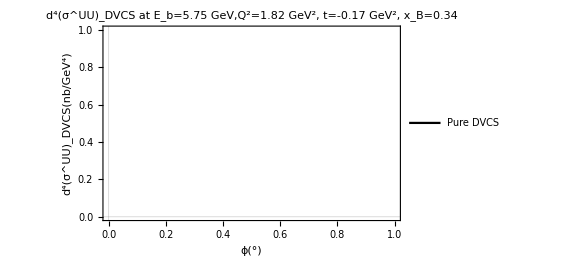

```mathematica
Plot[CrossSection,
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure DVCS"},
LegendLayout->{"Row",2}
],
{0.85,0.85}],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS(nb/GeV^4)"},
PlotStyle->{Black},
PlotLabel->"d^4(σ^UU)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->All,
PlotTheme -> "Scientific"]
```

```mathematica
hhh
```

hhh